Solve::optx: Unknown option PlotStyle in Solve[Tan[x], {x, -4\\ π, 4\\ π}, PlotStyle → InterpretationBox[ButtonBox[
TooltipBox[
RowBox[{
GraphicsBox[{
{GrayLevel[0], RectangleBox[{0, 0}]}, 
{GrayLevel[0], RectangleBox[{1, -1}]}, 
{RGBColor[1, 0, 0], RectangleBox[{0, -1}, {2, 1}]}},
AspectRatio->1,
Frame->True,
FrameStyle->RGBColor[0.6666666666666666, 0., 0.],
FrameTicks->None,
ImageSize->Dynamic[{Automatic, 1.35 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]}],
PlotRangePadding->None], ""}],
"RGBColor[1, 0, 0]"],
Appearance->None,
BaseStyle->{},
BaselinePosition->Baseline,
ButtonFunction:>With[{Typeset`box$ = EvaluationBox[]}, 
If[
Not[
AbsoluteCurrentValue["Deployed"]], SelectionMove[Typeset`box$, All, Expression]; FrontEnd`Private`$ColorSelectorInitialAlpha = 1; FrontEnd`Private`$ColorSelectorInitialColor = RGBColor[1, 0, 0]; FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; MathLink`CallFrontEnd[
FrontEnd`AttachCell[Typeset`box$, 
FrontEndResource["RGBColorValueSelector"], {0, {Left, Bottom}}, {Left, Top}, "ClosingActions" -> {"SelectionDeparture", "ParentChanged", "EvaluatorQuit"}]]]],
DefaultBaseStyle->{},
Evaluator->Automatic,
Method->"Preemptive"],
RGBColor[1, 0, 0],
Editable->False,
Selectable->False]]. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/General/optx",
ButtonNote->"Solve::optx"]

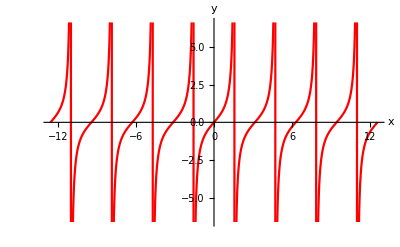

```mathematica
Plot[Tan[x], {x, -4Pi, 4Pi}, PlotStyle->Red, AxesLabel->{"x", "y"}]
```

```mathematica
pravidla = Solve[{2x1 + 3x2 + 4.2x3 ==5, 3x1 + 15.2 x2 + 8.7x3 == 80.1, 4x1 + 8.9x2 + 17.2x3 == 11}, {x1, x2, x3}]
```

{{x1→-3.63596,x2→7.29908,x3→-2.29174}}

```mathematica
Solve[-27+4 x+5 x^2 == 0,x] //N
```

{{x→-2.75797},{x→1.95797}}

```mathematica
mojefce[x_] := Sin[x^2]+ Cos[x]
```

```mathematica
mojefce[2]
```

Cos[2]+Sin[4]

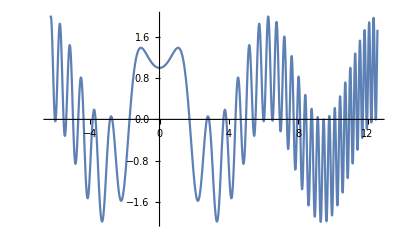

```mathematica
Plot[mojefce[x], {x, -2Pi, 4Pi}]
```

```mathematica
f[x_, y_] := x^2+ 2x*y + 2 y^2
```

```mathematica
Plot3D[f[x,y], {x, -4, 4}, {y, -6, 4}, AxesLabel->{"x", "y", "z"}]
```

-Graphics3D-

```mathematica
pole = {Skoda, Audi, BMW}
```

{Skoda,Audi,BMW}

```mathematica
Audi = {A4, A6, A8, R8, Q7}
```

{A4,A6,A8,R8,Q7}

```mathematica
pole
```

{Skoda,{A4,A6,A8,R8,Q7},BMW}

```mathematica
(* dela jednorozmerne pole *)
```

```mathematica
Flatten[pole]
```

{Skoda,A4,A6,A8,R8,Q7,BMW}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[5, 10]
```

{5,6,7,8,9,10}

```mathematica
Range[5, 15, 5]
```

{5,10,15}

```mathematica
Table[mojefce[x], {x, 1, 2}] //N
```

{1.38177,-1.17295}

```mathematica
pravidla = Solve[{2x1 + 3x2 + 4.2x3 ==5, 3x1 + 15.2 x2 + 8.7x3 == 80.1, 4x1 + 8.9x2 + 17.2x3 == 11}, {x1, x2, x3}]
```

{{x1→-3.63596,x2→7.29908,x3→-2.29174}}

```mathematica
pravidla
```

{{x1→-3.63596,x2→7.29908,x3→-2.29174}}

```mathematica
x1 /. pravidla
```

{-3.63596}

```mathematica
a /. pravidla
```

{a}

```mathematica
x1
```

x1

```mathematica
x1 + 2 x2 /.pravidla
```

{10.9622}

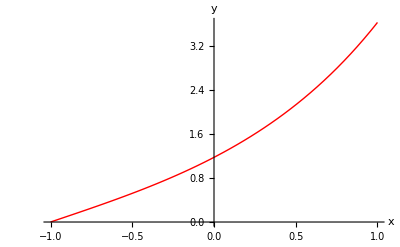

```mathematica
f[x_] := Sinh[x^2];
Plot[f[√(t+1)], {t, -1, 1}, AxesLabel->{"x", "y"}, PlotStyle->{Thick, Red}]
```